## Build Covariance Matrix

```mathematica
M = {{-(2*κ+k)/γ,0},{δ*κ/γ,-k/γ}};
```

```mathematica
MatrixForm[M]
```

((-k-2 κ)/γ | 0
(δ κ)/γ | -k/γ)

```mathematica
expM = MatrixExp[M*(t-tp)];
```

```mathematica
cov = Integrate[expM.{{4*T/γ,0},{0,T/(γ)*(1-δ^2)}}.Transpose[expM],{tp,-∞,t},Assumptions->{γ>0,k>0,κ>0}];
```

{{(2 T)/(k+2 κ),(T δ κ)/((k+κ) (k+2 κ))},{(T δ κ)/((k+κ) (k+2 κ)),1/2 T (1/k+δ^2 (-2/(k+κ)+1/(k+2 κ)))}}

```mathematica
cov = Simplify[cov]
```

{{(2 T)/(k+2 κ),(T δ κ)/((k+κ) (k+2 κ))},{(T δ κ)/((k+κ) (k+2 κ)),1/2 T (1/k+δ^2 (-2/(k+κ)+1/(k+2 κ)))}}

```mathematica
P[R_,r_,kk_] := Simplify[Exp[-1/2*{r,R}.Inverse[cov].{r,R}]]/.{k-> kk};
```

```mathematica
P[1,1,1]
```

ⅇ^(-((1+κ) (-5+δ^2+(-7+4 δ+3 δ^2) κ-2 κ^2))/(4 T (-1+δ^2+2 (-1+δ^2) κ-κ^2)))

## Patching and Normalisation

```mathematica
SubMinus[k]=2*Subscript[u, 0]/(L^2);
```

(2 u_0)/L^2

```mathematica
SubPlus[k]= 2*Subscript[u, 0]/(l^2);
```

(2 u_0)/l^2

```mathematica
SubMinus[f]= Simplify[Integrate[P[R,r,SubMinus[k]],{r,-∞,∞},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}];
```

-(ⅇ^(-(2 R^2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(L^2 T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √(2 π) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)

```mathematica
SubPlus[f]= Simplify[Integrate[P[R,r,SubPlus[k]],{r,-∞,∞},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}];
```

-(ⅇ^(-(2 R^2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(l^2 T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √(2 π) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)

```mathematica
SubMinus[int] = Simplify[Integrate[SubMinus[f],{R,-L,0},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0}]];
```

(L^2 π T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))])/(2 (L^2 κ+2 u_0) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))

```mathematica
SubPlus[int] = Simplify[Integrate[SubPlus[f],{R,0,l},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}]];
```

(l^2 π T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))])/(2 (l^2 κ+2 u_0) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{R-> 0})==SubPlus[A]*(SubPlus[f]/.{R-> 0}) && SubMinus[A]*SubMinus[int]+SubPlus[A]*SubPlus[int]==1,{SubMinus[A],SubPlus[A]}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,0<δ<1,T>0,l>0}];
```

{{A_-→(2 √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(L π T (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))),A_+→-((2 u_0 (l^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √((T (l^2 κ+u_0) (L^2 κ+u_0) (L^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))/(l π T (-4 (-1+δ^2) u_0^3 (L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))+l^2 L^2 κ^3 (L^3 Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l^3 Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))-2 (-1+δ^2) κ u_0^2 (L (l^2+3 L^2) Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l (3 l^2+L^2) Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))+κ^2 u_0 (L^3 (2 L^2-3 l^2 (-1+δ^2)) Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l^3 (2 l^2-3 L^2 (-1+δ^2)) Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0))))))}}

```mathematica
SubMinus[exprA]=SubMinus[A]->Simplify[(SubPlus[f]/(SubMinus[f]*SubPlus[int]+SubPlus[f]*SubMinus[int]))/.{R->0}];
```

A_-→(l √(2 π) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))))

```mathematica
SubPlus[exprA]=SubPlus[A]->Simplify[(SubMinus[f]/(SubMinus[f]*SubPlus[int]+SubPlus[f]*SubMinus[int]))/.{R->0}];
```

A_+→(L √(2 π) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))))

## Current

```mathematica
Subscript[J, R]= Simplify[-k*R/γ*P[R,r,k]+δ*κ*r/γ*P[R,r,k]-T*(1-δ^2)/(2*γ)*D[P[R,r,k],R]];
```

(ⅇ^(-((k+κ) (k^2 (-4 R^2+r^2 (-1+δ^2))+k (-4 R^2+4 r R δ+3 r^2 (-1+δ^2)) κ-2 r^2 κ^2))/(4 T (k^2 (-1+δ^2)+2 k (-1+δ^2) κ-κ^2))) δ κ (k^2 (r-r δ^2)+k (-2 R δ-3 r (-1+δ^2)) κ+2 r κ^2))/(2 γ (-k^2 (-1+δ^2)-2 k (-1+δ^2) κ+κ^2))

```mathematica
{{SubMinus[exprr]}}= FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->- L,k-> SubMinus[k]})==0,r],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0}];
```

{{r→-(2 L^3 δ κ u_0)/(L^4 κ^2-(-1+δ^2) u_0 (3 L^2 κ+2 u_0))}}

```mathematica
{{SubPlus[exprr]}}= FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R-> l,k-> SubPlus[k]})==0,r],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}];
```

{{r→(2 l^3 δ κ u_0)/(l^4 κ^2-(-1+δ^2) u_0 (3 l^2 κ+2 u_0))}}

```mathematica
Subscript[J, left]=Integrate[SubMinus[A]*Subscript[J, R]/.{R-> -L,k-> SubMinus[k],SubMinus[exprA]},{r,-∞,r/. SubMinus[exprr]},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}];
```

-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √(2 π) T δ κ (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(L^2 γ (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) (κ^2-(4 (-1+δ^2) κ u_0)/L^2-(4 (-1+δ^2) u_0^2)/L^4) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))))

```mathematica
Subscript[J, right]=Integrate[SubPlus[A]*Subscript[J, R]/.{R-> l,k-> SubPlus[k],SubPlus[exprA]},{r,r/.{SubPlus[exprr]},Infinity},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}];
```

(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √(2 π) T δ κ (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(l^2 γ (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) (κ^2-(4 (-1+δ^2) κ u_0)/l^2-(4 (-1+δ^2) u_0^2)/l^4) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))

```mathematica
Subscript[J, total]= Simplify[Subscript[J, left]+ Subscript[J, right],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0,l>0,SubPlus[k]>0}];
```

-((2 δ κ (-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))+(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))/(π γ ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))))

```mathematica
Subscript[J, total]=-((2 δ κ (-((ⅇ^(-(2 Subscript[u, 0] (L^2 κ+Subscript[u, 0]) (L^2 κ+2 Subscript[u, 0]))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))) L √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 l^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 l^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(l^2 κ+2 Subscript[u, 0])))/((L^2 κ+2 Subscript[u, 0]) (-l^4 κ^2+3 l^2 (-1+δ^2) κ Subscript[u, 0]+2 (-1+δ^2) Subscript[u, 0]^2)))+(ⅇ^(-(2 Subscript[u, 0] (l^2 κ+Subscript[u, 0]) (l^2 κ+2 Subscript[u, 0]))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 L^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 L^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(L^2 κ+2 Subscript[u, 0])))/((l^2 κ+2 Subscript[u, 0]) (-L^4 κ^2+3 L^2 (-1+δ^2) κ Subscript[u, 0]+2 (-1+δ^2) Subscript[u, 0]^2))))/(π γ ((L Erf[√2 √((Subscript[u, 0] (L^4 κ^2+3 L^2 κ Subscript[u, 0]+2 Subscript[u, 0]^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ Subscript[u, 0]-4 (-1+δ^2) Subscript[u, 0]^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 l^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 l^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(Subscript[u, 0] (L^2 κ+Subscript[u, 0]) (l^2 κ+2 Subscript[u, 0]))))/((L^2 κ+2 Subscript[u, 0]) (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))+(l Erf[√2 √((Subscript[u, 0] (l^4 κ^2+3 l^2 κ Subscript[u, 0]+2 Subscript[u, 0]^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ Subscript[u, 0]-4 (-1+δ^2) Subscript[u, 0]^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 L^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 L^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(Subscript[u, 0] (l^2 κ+Subscript[u, 0]) (L^2 κ+2 Subscript[u, 0]))))/((l^2 κ+2 Subscript[u, 0]) (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))))
```

-((2 δ κ (-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))+(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))/(π γ ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))))

## Simplifying Notation

```mathematica
Subscript[J, paper]=Simplify[Subscript[J, total]/.{T->T*Subscript[u, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[u, 0]/d^2},Assumptions->{γ>0,κ>0,Subscript[u, 0]>0,Subscript[λ, l]>0,Subscript[λ, r]>0,d>0,T>0,δ>0,Subscript[u, 0]>0}];
```

```mathematica
Subscript[J, unitless]=Simplify[ Subscript[J, paper]/.{T->(Subscript[T, 1]+Subscript[T, 2])/2,δ->(Subscript[T, 2]-Subscript[T, 1])/(Subscript[T, 1]+Subscript[T, 2])},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[u, 0]>0}];
```

```mathematica
forplot = Simplify[Subscript[J, unitless]/(Subscript[u, 0]/(γ*d))/.{d->1,Subscript[λ, r]->1-Subscript[λ, l]},{κ>0,Subscript[λ, l]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Subscript[u, 0]>0}]
```

```mathematica
Subscript[J, sub]= forplot/.{Subscript[λ, l]->0.1,Subscript[T, 1]->0.1,Subscript[u, 0]->1,Subscript[T, 2]->T};
```

## Plotting w.r.t data

```mathematica
v30 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k30.h5","vvals"];
```

```mathematica
v50 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k50.h5","vvals"];
```

```mathematica
v70 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/k70.h5","vvals"];
```

```mathematica
tvals = Array[# & ,40, {0.1,1}]
```

{0.1,0.123077,0.146154,0.169231,0.192308,0.215385,0.238462,0.261538,0.284615,0.307692,0.330769,0.353846,0.376923,0.4,0.423077,0.446154,0.469231,0.492308,0.515385,0.538462,0.561538,0.584615,0.607692,0.630769,0.653846,0.676923,0.7,0.723077,0.746154,0.769231,0.792308,0.815385,0.838462,0.861538,0.884615,0.907692,0.930769,0.953846,0.976923,1.}

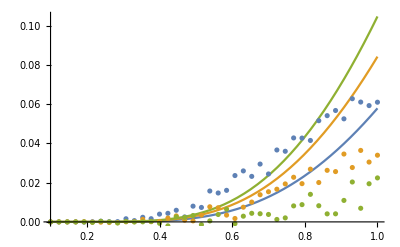

```mathematica
Show[{Plot[{Subscript[J, sub]/.{κ->30},Subscript[J, sub]/.{κ->50},Subscript[J, sub]/.{κ->70}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v30},Transpose@{tvals,-v50},Transpose@{tvals,-v70}}]}]
```

## Expansion in strong spring

```mathematica
Subscript[J, exp]= Subscript[J, paper]/.{κ->q*T};
```

```mathematica
Series[Subscript[J, exp],{q,∞,0}];
```

```mathematica
Simplify[-(2 (ⅇ^(-2/T) T δ Subscript[u, 0] (-√(q^3 T^4 Subscript[u, 0]^4 Subscript[λ, l]^6) Subscript[λ, r]^3+Subscript[λ, l]^3 √(q^3 T^4 Subscript[u, 0]^4 Subscript[λ, r]^6))) q)/(d^2 π γ Erf[√2 √(1/T)] (Subscript[λ, r]^3 √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^6 Subscript[λ, r]^2)+Subscript[λ, l]^3 √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^2 Subscript[λ, r]^6)))-1/(d^2 π γ)2 (T δ Subscript[u, 0] ((T^3 Subscript[λ, l]^4 Subscript[λ, r]^4 (-(ⅇ^(-2/T) √(q^3 T^4 Subscript[u, 0]^4 Subscript[λ, r]^6) (T Subscript[λ, l]^2+T δ^2 Subscript[λ, l]^2+4 T Subscript[λ, r]^2+12 δ^2 Subscript[λ, r]^2))/(2 T^5 Subscript[λ, l]^3 Subscript[λ, r]^6)+(ⅇ^(-2/T) √(q^3 T^4 Subscript[u, 0]^4 Subscript[λ, l]^6) (4 T Subscript[λ, l]^2+12 δ^2 Subscript[λ, l]^2+T Subscript[λ, r]^2+T δ^2 Subscript[λ, r]^2))/(2 T^5 Subscript[λ, l]^6 Subscript[λ, r]^3)))/(Erf[√2 √(1/T)] (Subscript[λ, r]^3 √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^6 Subscript[λ, r]^2)+Subscript[λ, l]^3 √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^2 Subscript[λ, r]^6)))-(ⅇ^(-2/T) T^3 Subscript[λ, l]^4 Subscript[λ, r]^4 (-√(q^3 T^4 Subscript[u, 0]^4 Subscript[λ, l]^6) Subscript[λ, r]^3+Subscript[λ, l]^3 √(q^3 T^4 Subscript[u, 0]^4 Subscript[λ, r]^6)) (-1/(2 T^4 Subscript[λ, l]^6 Subscript[λ, r]^3)ⅇ^(-2/T) √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^6 Subscript[λ, r]^2) (-6 √(2/π) √(1/T) δ^2 Subscript[λ, l]^2+ⅇ^(2/T) Erf[√2 √(1/T)] Subscript[λ, l]^2+4 ⅇ^(2/T) δ^2 Erf[√2 √(1/T)] Subscript[λ, l]^2+ⅇ^(2/T) Erf[√2 √(1/T)] Subscript[λ, r]^2+ⅇ^(2/T) δ^2 Erf[√2 √(1/T)] Subscript[λ, r]^2)-1/(2 T^4 Subscript[λ, l]^3 Subscript[λ, r]^6)ⅇ^(-2/T) √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^2 Subscript[λ, r]^6) (ⅇ^(2/T) Erf[√2 √(1/T)] Subscript[λ, l]^2+ⅇ^(2/T) δ^2 Erf[√2 √(1/T)] Subscript[λ, l]^2-6 √(2/π) √(1/T) δ^2 Subscript[λ, r]^2+ⅇ^(2/T) Erf[√2 √(1/T)] Subscript[λ, r]^2+4 ⅇ^(2/T) δ^2 Erf[√2 √(1/T)] Subscript[λ, r]^2)))/(Erf[√2 √(1/T)]^2 (Subscript[λ, r]^3 √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^6 Subscript[λ, r]^2)+Subscript[λ, l]^3 √(q^4 T^5 Subscript[u, 0]^4 Subscript[λ, l]^2 Subscript[λ, r]^6))^2))),{q>0,Subscript[λ, l]>0,Subscript[λ, r]>0,T>0,Subscript[U, 0]>0,δ>0}]
```

(ⅇ^(-2/T) δ (-12 δ^2+T (-3+δ^2)) u_0 (λ_l-λ_r))/(d^2 π √(q T^3) γ Erf[(√2)/(√T)] λ_l^2 λ_r^2)